# Helpful Guide to Mathematica

## Contents

Tricks & Shortcuts

Greek alphabet keyboard shortcuts

Equation formatting

Superscript

Subscript

Square root

Divided by

Shortcut to comment out blocks of code

Common Mistakes

Defining functions

Evaluating a function at a specific value (from NDSolve or similar)

Evaluating a function at a specific value (not from NDSolve)

Formatting

General

Setting font and font size

Plotting

Frame and frame labels

Line styles

Plot legend - labeling curves

Plot labels

Image size and padding

Shortcut for plot formatting options

Plot for different values of a parameter

Graphics

Adding arrows to a plot

Creating images/diagrams using Graphics

Rectangles

Arrows

Displaying text inside a shape

Adding Graphics to plots

Adding labels to curves (above, next to, etc.)

Adding labels onto curves (on curve itself)

Adding tables and text to plots

Adding Graphics to plots using Scaled[ ]

Text options

Manipulate Controls

Making variables inactive

Labeling Manipulate variables

Incorporating text into the Manipulate window

Creating multiple Manipulate windows (PaneSelector)

Making a vertical slider

Putting controls into columns

Continuous updating of ‘Manipulate’ variables

Visually separating variables in the ‘Manipulate’ window (Delimiter)

Commonly used Commands in Demonstrations

Solving ordinary differential equations (ODE)

Defining equations for NDSolve (method #1)

Entering ODE’s into NDSolve (method #2)

Manipulate

Localizing variables (Module)

Setup for making buttons for multiple plots (Switch)

Show multiple plots on same axes

Miscellaneous

Entering constants, equations, and functions

If statements

Control number of digits displayed

Select a solution from a list *important*

Localize variables for faster evaluations

Partial Differential Equations (PDE)

Writing PDE’s in Mathematica

Solving PDE’s in Mathematica

Nonlinear Models

Nonlinear fit of data to rate law

Fitting the model

Plotting the residuals

3D Plot and points

Nonlinear fit of data

No scatter example

What You Need Before Submitting

Troubleshooting Tips

## Tricks & Shortcuts

This guide is meant to be an additional resource for you to help with your demonstrations. The majority of the functions and commands in this guide are described in a way that relate more to making an interactive simulation in Mathematica. For more information on each command, how they are formatted, and more of what you can do with them, please look through the Documentation Center in the Help menu.

### Greek alphabet keyboard shortcuts

Most Greek letters correspond directly to the English alphabet, others need to be spelled out, "ESC" + English letter + "ESC". Here are a few examples:
ESC + "a" + ESC generates α
ESC + "r" + ESC generates ρ
ESC + "th" + ESC generates θ
ESC + “d” + ESC generates δ
ESC + “pd” + ESC generates ∂
To get an uppercase Greek letter just use "SHIFT" before the English letter
ESC + "D" + ESC generates Δ

### Equation formatting

Getting equations out of straight line format so your code is easier to read. You can also use one of the palettes in Mathematica but this may be quicker.

#### Superscript

Hold “CTRL” + “6” to quickly get a superscript
The right arrow will bring you out of it.
10^10 becomes 10^10

#### Subscript

Hold “CTRL” + “-“ to get a subscript
C_A becomes C_A

#### Square root

Hold “CTRL” + “2” to start entering values/equations under the square root. 
The right arrow key will bring you out of it
x^1/2 becomes √x

#### Divided by

Highlight everything in the numerator and with those values/variables selected hold “CTRL” + “/” and release, highlight the expression you want to stay in the numerator.
(x+y)/(10*x-y) becomes (x+y)/(10*x-y)

## Common Mistakes

### Defining functions

Defining a function in terms of a variable when that variable appears nowhere in the equation. For example:

```mathematica
f[x_]=g[x]/2;
```

The function f does not directly contain the variable x, g[x] is a function of x but f isn’t, so we write it like this:

```mathematica
f=g[x]/2;
```

### Evaluating a function at a specific value (from NDSolve or similar)

This depends on how you got the function you are evaluating, if the function (let’s say g[x]) was obtained by solving an ODE you have to evaluate it differently at a specific value of x, let’s evaluate g[x] at x=2.

```mathematica
s=NDSolve[{
g'[x]==x+2,
g[0]==10},g,{x,0,10}]
```

{{g→InterpolatingFunction[{{0.,10.}},<>]}}

You get some function g[x]. Here are two easy ways to solve g[x] at x=2, both methods work well and neither is better than the other. You may choose one over the other depending on what you are trying to do with your code.

1. Evaluate g[x] at s for x=2

```mathematica
g[x]/.s/.x->2
```

{16.}

2. Evaluate g[2] at s

```mathematica
g[2]/.s
```

{16.}

You can also evaluate g[x] at a list of values, either of the above methods can be used for this.

```mathematica
g[x]/.s/.x->{2,3,4,5}
```

{{16.,20.5,26.,32.5}}

### Evaluating a function at a specific value (not from NDSolve)

If a function has already been defined and we didn’t need to use NDSolve (or similar) to get a solution to the equation, then evaluating the function at a specific value is very similar to the above methods. The one notable difference is you don’t have to evaluate the function at the solution to NDSolve.

```mathematica
h[x_]=x^2+2*x+1;
h[x]/.x->5
```

36

```mathematica
h[5]
```

36

You can also evaluate the function at a list of values. Then if you needed to extract one value from this list, write which component (1 for first, 2 for second, etc.) in double square brackets at the end of the expression.

```mathematica
h[x]/.x->{2,3,4,5}
```

{9,16,25,36}

```mathematica
h[{2,3,4,5}][[2]]
```

16

## Formatting

Formatting is necessary for all good, valuable demonstrations. If your demonstration does not contain any of the following formatting options (or similar), it would be a good idea to add them in order to help you’re demonstration stand out from the others. The goal is to format it in such a way that not only makes your demonstration standout, but also translates your concept or idea well.

### General

#### Setting font and font size

This can also be done inside the Plot command. Changing the font type is not advised if you are submitting your demonstration to the Wolfram Demonstrations Project.

```mathematica
SetOptions[Plot,LabelStyle->{FontFamily->"Arial",FontSize->16}];
```

### Plotting

#### Frame and frame labels

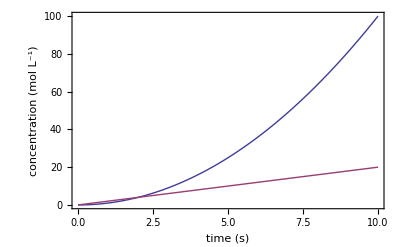

```mathematica
Plot[{t^2,2*t},{t,0,10},
Frame->True,
FrameLabel->{"time (s)","concentration (mol L^-1)"},
LabelStyle->16]
```

#### Line styles

If there is only one curve then only one set of curly brackets { } is needed after PlotStyle.

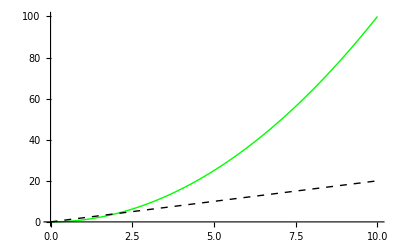

```mathematica
Plot[{t^2,2*t},{t,0,10},
PlotStyle->{{Green,Thick},{Black,Thick,Dashed}}]
```

#### Plot legend - labeling curves

Commands in italics are not necessary, but are encouraged.

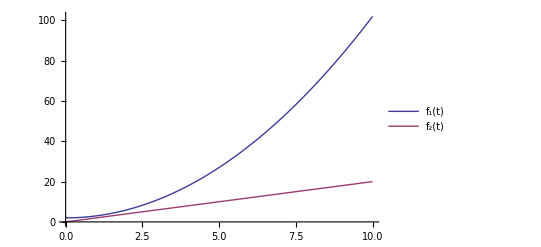

```mathematica
Plot[{t^2+2,2*t},{t,0,10},
PlotLegends->
Placed[
LineLegend[{"f_1(t)","f_2(t)"}],
Above]]
```

#### Plot labels

Style is used so you can easily set a font size or type. “16” is the equivalent of FontSize→16 here.

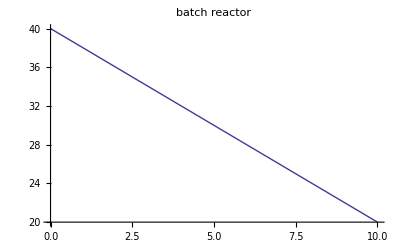

```mathematica
Plot[-2*t+40,{t,0,10},
PlotLabel->Style["batch reactor",16]]
```

#### Image size and padding

ImagePadding prevents a plot from “jiggling”. Often when using Manipulate, as you move the slider, the axes on the plot change as the function is being evaluated. You’ll see that the values on the vertical axis change and depending on the sig figs, it will look like the numbers are pushing on the plot frame, making the plot “jiggle”. 
Adding ImagePadding basically prevents the plot from expanding/contracting by setting a boundary between the edge of the plot and the bounds of the ImageSize. Think of it like adding a mat board to a picture frame so the picture sits in the frame nice and snug even if the frame is otherwise too big for the picture. Unless you set a PlotRange, you should add ImagePadding before submitting your demonstration.

```mathematica
Plot[f[t],{t,0,10},
	PlotRange->All,
	Frame->True,
	ImageSize->{horizontal length,vertival length},
	ImagePadding->{{left bound,right bound},{bottom bound, top bound}}]
```

```mathematica
Manipulate[
Module[{sm},
sm=NDSolve[{
Ca'[t]==-0.1*Ca[t],
Ca[0]==Cao},Ca,{t,0,10}];
Plot[Ca[t]/.sm,{t,0,10},
PlotRange->All,
Frame->True,
ImageSize->{350,200},
ImagePadding->{{20,15},{25,10}}](*{{left,right},{bottom,top}}*)
],
{{Cao,2,"initial concentration of A"},1,5,0.5}]
```

#### Shortcut for plot formatting options

If you have multiple plots that all have the same formatting options, you can use this trick to define all of them and then call on this command in each plot. This will save time if you need to change your plot formatting options, instead of changing them in every Plot function, you can change it once using this trick. 
You can have more than one set of options too, just name the Sequence something different (specs2, specs3, etc.)

```mathematica
specs=Sequence[(*Sequence will lump a series of arguments together to be used in a function*)
	plot formatting options];(*enter options here as you would normally do inside Plot*)
Plot[function[x],{x,Subscript[x, min],Subscript[x, max]},Evaluate@specs](*instead of putting formatting options after the x-range, say Evaluate@specs*)
```

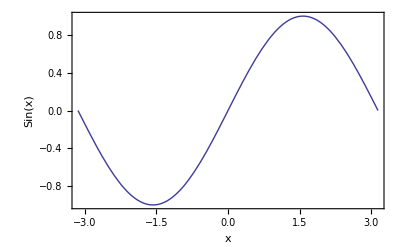

```mathematica
Module[
{specs},
specs=Sequence[
Frame->True,
FrameLabel->{"x","Sin(x)"}];
Plot[Sin[x],{x,-π,π},Evaluate@specs]
]
```

### Plot for different values of a parameter

If you have a function of x and y (which will produce a 3D plot) you can select different values of a single variable to plot if you want a 2D plot instead.

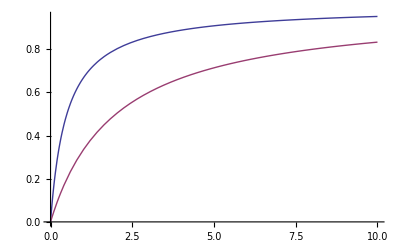

```mathematica
f[x_,y_]=(y*x)/(1+y*x);
Plot[{f[x,2],f[x,0.5]},{x,0,10}]
```

## Graphics

### Adding arrows to a plot

Write the Plot function as you normally would and use PlotStyle to add the arrows. The command should be entered the following way:

```mathematica
PlotStyle->Arrowheads[
Prepend[ConstantArray[size of arrowheads,#of arrowheads],
element to be prepended (*arrows start at beginning or end of function*)]]
```

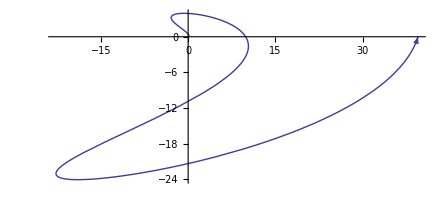

```mathematica
ParametricPlot[{t^2*Cos[2*t],t^2*Sin[t]},{t,0,2*Pi},
PlotStyle->Arrowheads[
Prepend[ConstantArray[0.05,5],0]]
]/.Line->Arrow
```

### Creating images/diagrams using Graphics

Use the following to create diagrams to add to your demonstration.

#### Rectangles

```mathematica
Graphics[{
{(*Add in any formmating here followed by the shape, here are a few examples*)
EdgeForm[Formatting for the border],
FaceForm[Formatting for inside the rectangle or shape],
Rectangle[{Subscript[x, min],Subscript[y, min]},{Subscript[x, max],Subscript[y, max]}]
}
},
PlotRange->{{Subscript[x, bound,min],Subscript[x, bound,max]},{Subscript[y, bound,min],Subscript[y, bound,max]}}]
```

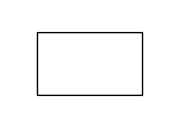

```mathematica
Graphics[{
{EdgeForm[AbsoluteThickness[1]],
FaceForm[None],
Rectangle[{0,0},{0.5,0.3}]
}
},
PlotRange->{{-0.1,0.6},{-0.1,0.4}},
ImageSize->Small]
```

#### Arrows

```mathematica
Graphics[{
{Arrowheads[size of arrowhead],
	Arrow[{{Subscript[x, tail],Subscript[y, tail]},{Subscript[x, head],Subscript[y, head]}}]
	}
},
PlotRange->{{-0.1,1.1},{-0.1,0.1}}]
```

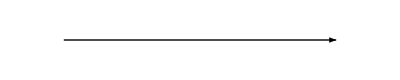

```mathematica
Graphics[{
{Arrowheads[0.05],
Arrow[{{0,0},{1,0}}]
}
},
PlotRange->{{-0.1,1.1},{-0.1,0.1}}]
```

#### Displaying text inside a shape

Approach #1
You will make a rectangle (or other shape) as you normally would, then to add text add the following highlighted command inside a new set of curly brackets { }. The way the Text command is formatted below is just a suggestion, writing it out this way will allow you to control the font size, face, color, etc. of the text.

```mathematica
Graphics[{
	{(*add in any additional formatting to the shape here*)
	Rectangle[{Subscript[x, min],Subscript[y, min]},{Subscript[x, max],Subscript[y, max]}]
	},
	{Text[Style["text to be displayed",formatting to text is added here],
		{Subscript[x, position],Subscript[y, position]}]
	}
},ImageSize->Small]
```

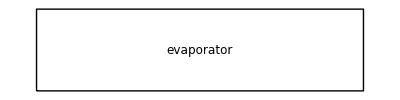

```mathematica
Graphics[{
{EdgeForm[AbsoluteThickness[1]],
FaceForm[None],
Rectangle[{0.3,0.6},{0.5,0.65}]
},
{Text[Style["evaporator",12],
{0.4,.625}]
}
},
ImageSize->Tiny]
```

Approach #2

```mathematica
Graphics[{
	{(*add in additional formatting to shape here*)
	Rectangle[{Subscript[x, min],Subscript[y, min]},{Subscript[x, max],Subscript[y, max]}]},
	{Inset[
	Cell["text to be displayed",TextAlignment->Center],
	{Subscript[x, position],Subscript[y, position]}
	]
	}
},ImageSize->Tiny]
```

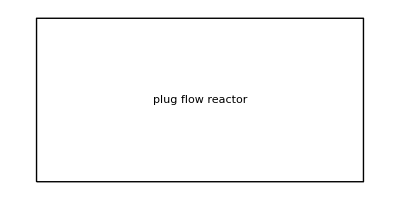

```mathematica
Graphics[{
{EdgeForm[AbsoluteThickness[1]],
FaceForm[None],
Rectangle[{0,0},{3,1.5}]},
{Inset[
Cell["plug flow reactor",TextAlignment->Center],
{1.5,0.75}
]
}
},
ImageSize->Tiny]
```

### Adding Graphics to plots

#### Adding labels to curves (above, next to, etc.)

Combine Plot (or similar) and Graphics by naming each function and then using Show to combine them. The method shown below is just one way of doing this.

```mathematica
(*'Style' will allow you to easily control the font, face, etc. of the test*)
labels=Graphics[{
	Text[Style["1^st label",formatting],{Subscript[x, position],Subscript[y, position]},{Subscript[x, offset],Subscript[y, offset]}],
	Text[Style["2^nd label",formatting],{Subscript[x, position],Subscript[y, position]},{Subscript[x, offset],Subscript[y, offset]}],
	Text[Style["3^rd label",formatting],{Subscript[x, position],Subscript[y, position]},{Subscript[x, offset],Subscript[y, offset]}]
}];
(*Offset isn't necessary but here is the format if you want to use it. 
	{0,0}  -> text centered at {x,y}
	{-1,0} -> left-hand end at {x,y}
	{1,0}  -> right-hand end at {x,y}
	{0,-1} -> centered above {x,y}
	{0,1}  -> centered below {x,y}*)
```

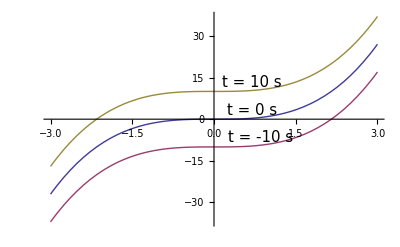

```mathematica
f[x_,t_]=x^3+t;
curves=Plot[{f[x,0],f[x,-10],f[x,10]},{x,-3,3}];
labels=Graphics[{
Text[Style["t = 10 s",15],{0.7,f[0.7,10]},{0,-1}],
Text[Style["t = 0 s",15],{0.7,f[0.7,0]},{0,-1}],
Text[Style["t = -10 s",15],{0.85,f[0.85,-10]},{0,-1}]
}];
Show[curves,labels]
```

#### Adding labels onto curves (on curve itself)

```mathematica
Plot[g[x],{x,Subscript[x, min],Subscript[x, max]},
	Epilog->
		Inset[
			Style["label",formatting],
			{Subscript[x, position],Subscript[y, position]},Background->color behind the label]
]
```

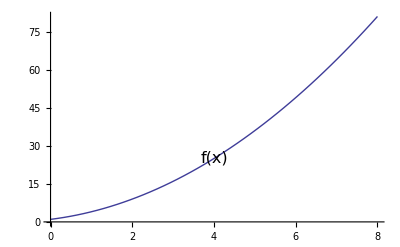

```mathematica
g[x_]=x^2+2*x+1;
Plot[g[x],{x,0,8},
Epilog->
Inset[
Style["f(x)",16],
{4,g[4]},Background->White]
]
```

#### Adding tables and text to plots

```mathematica
table=Graphics[{
	Inset[
		Grid[
			{{cell 1a,cell 2a},
			{cell 1b,cell 2b}},
		 Alignment->how cells should be aligned (see below for options),
		 Frame->what cells have a border (see below for options)
		]
	]
}];
Plot[y,{x,0,6},
	Epilog->
		Inset[table,{Subscript[x, position],Subscript[y, position]}]]
(*Alignment options:
	Left   -> left alighned
	Right  -> right aligned
	Top    -> aligned at top
	Bottom -> aligned at bottom
	Center -> center aligned
	x      -> aligned at position x from -1 (left) to +1 (right)
	{x,y}  -> aligned at horizontal and vertical positions x and y from -1 to +1
	"c"    -> aligned at a specific caracter or value in the grid
Frame options:
	{All,False} -> frames at all horizontal positions (columns)
	{False,All} -> frames at all vertical positions (rows)
for more Frame options, search 'Grid' in the Documentation Center*)
```

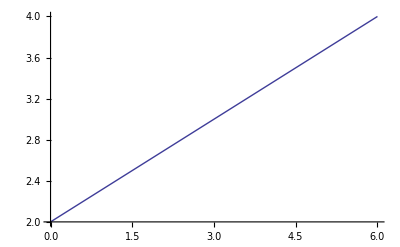

```mathematica
A=1;B=3;
y=A/B*x+2;
table=Graphics[{
Inset[
Grid[
{{"A =",A},
{"B =",B}},
Alignment->"=",
Frame->{False,All}
]
]
}];
Plot[y,{x,0,6},
Epilog->
Inset[table,{4,2.5}]]
```

#### Adding graphics to plots using Scaled[ ]

This one is almost the same as the one described above, you can also add graphics to a plot by following the guide above. In this example Scale is used in order to set the placement of the graphic (or table, or text, both are Graphics primitives). Using Scaled is helpful especially if your axis is changing as the sliders are moved, or if you end up changing your fixed plot range later on, your graphic will still show up in the same spot. Scaled is basically saying how far down the x- and y-axis will the graphic be placed.

```mathematica
pfr=Graphics3D[{
	{Arrow[{{0,0,0},{1,0,0}}]},
	{Cylinder[{{1,0,0},{3,0,0}},radius]},
	{Arrow[{{3,0,0},{4,0,0}}]}
	},
PlotRange->{{0,5},{0,0},{0,0}},
Boxed->False,
ViewPoint->{Subscript[x, view],Subscript[y, view],Subscript[z, view]}];
(*ViewPoint is used in this graphic, this will set the orientation of the graphic. The Documentation Center has a table of possible viewpoints and what they will do*)

Plot[π/4 Dr^2,{Dr,1,5},
	Epilog->
		Inset[name of graphic,Scaled[{Subscript[x, position,scaled],Subscript[y, position,scaled]}]
			]
	]
(*Here Scaled is placing the graphic 'pfr' x% of the way down the x-axis and y% of the way up the y-axis. The {x,y} position inside Scaled will (each) be less than 1.
```

```mathematica
pfr=Graphics3D[{
	{Arrow[{{0,0,0},{1,0,0}}]},
	{Cylinder[{{1,0,0},{3,0,0}},1]},
	{Arrow[{{3,0,0},{4,0,0}}]}
	},
PlotRange->{{0,5},{0,0},{0,0}},
Boxed->False,
ViewPoint->{2,-2,1}];

Plot[π/4 Dr^2,{Dr,1,5},
	Epilog->
		Inset[pfr,Scaled[{0.25,0.35}]
]
]
```

-Graphics-

### Text options

Text offset is explained above in Adding labels to curves, to change the direction the test is displayed in another specification is added after offset.

```mathematica
Text["text to display", position, offset , direction]
(*
direction specifications:
{1,0}   standard, horizontal
{1,1}   at an angle
{0,1}   vertical
{-1,-1} at an angle, flipped
*)
```

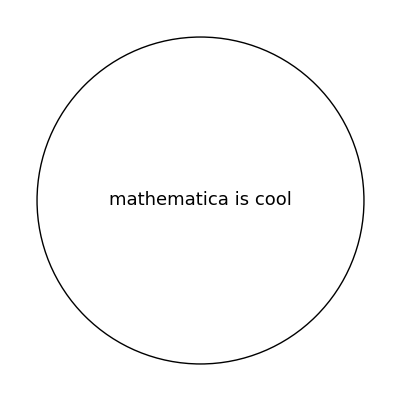
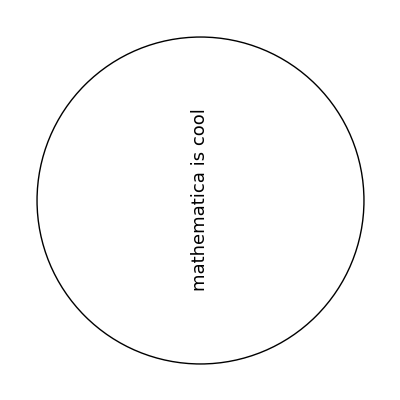
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
Graphics[{
Text[Style["mathematica is cool",18],{0,0},Automatic,d],
Circle[]
}],
{d,{{1,0},{1,1},{0,1},{-1,-1}}}
]
```

## Adding Graphics to plots

## Manipulate controls

### Making manipulated variables inactive

Below is an example of If and Enabled being used in a demonstration. Here If and Enabled are used to make a button inactive so the user can’t use it under certain conditions. The  portion of the code that is relevant here is highlighted in yellow. The slider for amplitude (a) becomes inactive when the Cosine plot is selected since this particular function does depend on the variable amplitude. Making the variable inactive for a certain condition will eliminate any confusion.

```mathematica
Manipulate[
Module[{f,g,p1,p2},
f[t_]=a*Sin[ω*t];
g[t_]=Cos[ω*t];
p1=Plot[f[t],{t,0,2*π},Frame->True,PlotRange->{-2,2}];
p2=Plot[g[t],{t,0,2*π},Frame->True];
Switch[atl,
1,Show[p1],
2,Show[p2]]],
{{atl,1,""},{
1->"Sin(t)",
2->"Cos(t)"},ControlType->SetterBar},
{{ω,1,"frequency"},0.5,5,0.1},
{{a,2,"amplitude"},0.25,2,0.25,Enabled->If[atl==1,True,False]}
]
```

### Assigning labels to Manipulate variables

When you use Switch, for example, with the intention of creating labeled buttons for different plots, you’ll also use this. However, if you just want to assign a name or a label to different values of a manipulated variable, Switch is not needed.

```mathematica
Control[{{var,Subscript[var, 0],"var name"},{
	Subscript[val, 1]->"label_1",
	Subscript[val, 2]->"label_2",
	Subscript[val, 3]->"label_3"},ControlType->control}]
```

```mathematica
Manipulate[
Module[
{F,p},
F[x_]=x+b;
p=Plot[F[x],{x,0,5},
PlotRange->{1,5},
Frame->True
]
],
{{b,1.5,"intercept"},{
1.5->"b1",
2.5->"b2",
3.5->"b3"},ControlType->SetterBar}]
```

### Incorporating text into the Manipulate window

```mathematica
Column[{
	"line 1",
	Control[{{Subscript[var, 1],Subscript[var, 1,0],"var_1 name"},Subscript[var, 1] range}], (*if you only want to have a heading above your variable, stop here*)
		Row[{                                       (*this is an example of incorporating other styles/layouts into the Manipulate window*)
		Control[{{Subscript[var, 2],Subscript[var, 2,0],"var_2 name"},Subscript[var, 2] range}],
		"line 2"
	}]
}]
```

```mathematica
Manipulate[
Module[{f},
f[x_]=a*x^2+b*x+c;
Plot[f[x],{x,-5,5},
Frame->True]
],
Column[{
Style["choose a value for 'a'",15],
Control[{{a,0.5,"a"},0.1,5,0.1,Appearance->"Labeled"}],
Style["choose a value for 'b'",15],
Control[{{b,1,"b"},0,2,0.1,Appearance->"Labeled"}],
Style["choose a value for 'c'",15],
Row[{
Control[{{c,0.5,"c"},0,3,0.1,Appearance->"Labeled"}],
Style["y-intercept",15]
}]
}]
]
```

### Creating multiple Manipulate windows (PaneSelector)

PaneSelector can be used here if, for example, you have more than one plot (or graphic) and you want some controls to be visible when one plot is shown and other controls visible when the other plot is selected. Instead of making some manipulated variables inactive you want them to disappear, this can be done by creating an option for another Manipulate window. In the code below, there are two plots (Sine or Cosine). Notice that the variable “a” (amplitude) has no effect on the behavior of the cosine function so a second window option was made where the control for “a” disappears.

```mathematica
PaneSelector[{
	1 -> Column[{(*this will keep all your controls organized*)
		Control[{{ctrl,1,""},{1->"pane 1",2->"pane 2"},ControlType->choose type}],(*this will let you switch between panes/windows*)
		Control[{{control #1...}}]
	}],
	2 -> Column[{
		Control[{{ctrl,1,""},{1->"pane 1",2->"pane 2"},ControlType->choose type}],(*keep this is both panes or else the buttons will 
																					disappear when you select the other option*)
		Control[{{control #2...}}]
	}]
},Dynamic@ctrl](*or whatever dummy control name used to distinguish between windows*)
(*this is saying that if ctrl = 1 then the control for crtl and control #1 will be visible and available and if ctrl = 2 is selected, 
	then the control for ctrl and control #2 will be available*)
```

The control that allows you to switch between different windows (different controls available/visible) is exactly like the control for Switch. In the example below “atl” is also part of Switch (before the controls) and is used to select different windows. You can also create a new dummy variable like “atl” inside PaneSelector that allows the user to select different windows. 

Please note that the window sizes may be slightly different depending on the controls in each. If you want to submit a demonstration containing this command, please use ImageSize to adjust the window sizes so that when you switch between them, their sizes do not change. In the example below you will notice that the window sizes are different.

```mathematica
Manipulate[
Module[{f,g,p1,p2},
f[t_]=a*Sin[ω*t];
g[t_]=Cos[ω*t];
p1=Plot[f[t],{t,0,2*π},Frame->True,PlotRange->{-2,2}];
p2=Plot[g[t],{t,0,2*π},Frame->True];
Switch[atl,
1,Show[p1],
2,Show[p2]]],
(* below is the portion of code you will need *)
PaneSelector[{
1->Column[{
Control[
{{atl,1,""},{
1->"Sin(t)",
2->"Cos(t)"},ControlType->SetterBar}],
Control[
{{ω,1,"frequency"},0.5,5,0.1}],
Control[
{{a,2,"amplitude"},0.25,2,0.25}]
}],
2->Column[{
Control[
{{atl,1,""},{
1->"Sin(t)",
2->"Cos(t)"},ControlType->SetterBar}],
Control[
{{ω,1,"frequency"},0.5,5,0.1}]
}]
},Dynamic@atl]
]
```

In order to make a window-in-a-window, insert another Switch inside the the ‘main’ Switch. Looking at the example above, the ‘main’ Switch is called “atl”.

```mathematica
Manipulate[
Switch[omm,
1,
Switch[ptv,
1,Show[Plot[Sin[x],{x,-π,π}]],
2,Show[Plot[Cos[x],{x,-π,π}]]
],
2,
Switch[twa,
1,Show[Plot[Log[x],{x,0,5}]],
2,Show[Plot[Exp[x],{x,0,5}]]
]
],
PaneSelector[{
1->Column[{
Control[{{omm,1,""},{1->"trig functions",2->"log functions"},PopupMenu}],
Control[{{ptv,1,""},{1->"sin(x)",2->"cos(x)"},SetterBar}]
}],
2->Column[{
Control[{{omm,1,""},{1->"trig functions",2->"log functions"},PopupMenu}],
Control[{{twa,1,""},{1->"ln(x)",2->"ⅇ^x"},SetterBar}]
}]
},Dynamic@omm]
]
```

### Making a vertical slider

```mathematica
Control[{{x,2,"x"},0,10,1,ControlType->VerticalSlider}]
```

### Putting controls into columns

```mathematica
Grid[{
	{Control[{{Subscript[var, (1,1)]..}}] , Control[{{Subscript[var, (2,1)]..}}]},
	{Control[{{Subscript[var, (1,2)]..}}] , Control[{{Subscript[var, (2,2)]..}}]}
	}]
(*
(1,1) refers to the position in column #1, row #1
(2,1) refers to the position in column #2, row #1
*)
```

```mathematica
Manipulate[
Plot[A*Sin[ω*t],{t,t1,t2},PlotRange->{{-2*π,2*π},{-2,2}}],
Grid[{
{"function specifications:\n","plotting limits:\n"},
{Control[{{A,1,"amplitude"},0.25,2}],Control[{{t1,-π,"lower limit"},-2*π,0,π/4}]},
{Control[{{ω,1,"frequency"},0.25,5}],Control[{{t2,π,"upper limit"},π/4,2*π,π/4}]}
}],ControlPlacement->Above,Alignment->Center]
```

### Continuous updating of ‘Manipulate’ variables

ContinuousAction→False will prevent Manipulate from updating continuously, instead it will update once the slider has been released.

```mathematica
Manipulate[
Plot[A*ⅇ^x,{x,0,1},PlotRange->{0,6}],
{{A,1.75,"amplitude"},0.5,2,0.25},ContinuousAction->False]
```

### Visually separating variables in the ‘Manipulate’ window (Delimiter)

Delimiter will but a faint line in the Manipulate window wherever it was placed in the code. It’s a nice way of organizing Manipulate variables in the window.

```mathematica
Manipulate[
Plot[{A*Sin[ωs*t],B*Cos[ωc*t]},{t,-π/2,π/2},Frame->True],
Style["ampitudes:",13,Bold],
{{A,1,"sine"},0.25,2},
{{B,1.5,"cosine"},0.25,3},
Delimiter,
Style["frequency:",13,Bold],
{{ωs,2,"sine"},0.1,2},
{{ωc,1,"cosine"},0.1,2}]
```

## Commonly used commands in demonstrations

This section is a brief overview of some essential commands and functions you will be using in your demonstrations, including Manipulate.

### Solving ordinary differential equations (ODE)

#### Defining equations for NDSolve, one method

When using NDSolve to solve a system of ODE’s, you’ll enter your differential equations first, then the conditions, followed by the variables and range. You can either enter all this directly inside NDSolve or you can name each section and enter that into NDSolve. Below is an example of the second method being used. Remember, if you choose this method the names you give the sets of equations are up to you, they can be anything.

```mathematica
ode={
f'[t]==f0*(1-f[t]),
g'[t]==g0
};
conditions={
f[0]==f0,
g[0]==g0
};
variables={f,g};
NDSolve[{
ode,
conditions},
variables,{t,0,10}];
```

Note that all equations entered are inside a set of curly brackets { } and followed by a semicolon. The curly brackets indicate that this is a list of equations and the semicolon will suppress each function, meaning once you enter this data (SHIFT+ENTER) there will be no output.
All “=” signs INSIDE NDSolve are actually double equal signs “==”.

#### Entering ODE’s into NDSolve

If you don’t want to define each set of equations to be entered into NDSolve as was shown above, the differential equations, conditions, and variables can be entered directly into NDSolve.

```mathematica
solution=NDSolve[{
f'[t]==f0*(1-f[t]),
g'[t]==g0,
f[0]==f0,
g[0]==g0},{f,g},{t,0,10}];
```

Above, each NDSolve function was defined as solution=NDSolve[{, this is a helpful way to define the solution to a function you wish to plot later on. How this will be used is discussed later on.

### Manipulate

All your functions will go inside Manipulate, below all functions except for Plot are suppressed with a semicolon. The manipulated variable, in this case it’s τ, is located inside a set of curly brackets. Note that the range of this variable on the slider is 1 ≤ τ ≤ 10 s with a step size (or increment) of 1. It is not necessary to include an increment, however it’s good to have one in your demonstration so you can set the number of digits displayed for the manipulated variable next to the slider. As shown below, to display the value of the manipulated variable add in Appearance→”Labeled”.

```mathematica
Manipulate[
Module[{sol},
sol=NDSolve[{
Ca'[t]==1/τ*(1-Ca[t])-0.2*Ca[t],
Ca[0]==1},Ca,{t,0,10}];
Plot[Ca[t]/.sol,{t,0,10}]],
{{τ,5,"residence time (s)"},1,10,1,Appearance->"Labeled"}]
```

### Localizing variables (Module)

You should have this command in all of your demonstrations. Basically what it does is allow you to localize all of your set variables (variables followed by an “ = ” sign). In the example below, you’ll see that the two declared variables (a and b) are now green, meaning that they have been localized inside Module. Once your demonstration has been put into demonstration format and all snapshots and the thumbnail have been added, make sure they are not being evaluated. If they are, you’ll notice that the (normally solid blue) bracket to the left of the code or image will be blinking. This is essentially saying that not all the variables are localized.

```mathematica
Manipulate[
Module[{a,b},
	a=1; b=2;
	Plot[a*x^b+c,{x,0,5}]
	],
{{c,0,"y-intercept"},0,10}
]
```

There are three ways to localize variables (Module, Block, and With), Block and With are shown below. For a detailed explanation of what each does and the differences between them, see this post on Stack Exchange.

### Setup for making buttons for multiple plots (Switch)

Switch is used inside Manipulate as a way to switch between multiple plots or graphics. This will create buttons or a drop-down list linked to a specific plot.

```mathematica
Manipulate[
p1=Plot[x^2+1,{x,-5,5}];
p2=Plot[2*x,{x,0,5}];
Switch[ctrl,(*this name can be anything*)
1,Show[p1],
2,Show[p2] (*associate "1" with p1 and "2" with p2*)
],
{{ctrl,1,""},{
1->"x^2+1",(*add labels to "1" and "2"*)
2->"2 x"},ControlType->Setter}]
```

### Show multiple plots on same axes

Use Show to display more than one Plot or Graphic together (on top of each other). Any type of Plot can be used, however for multiple plots the range of each should be the same. Plotting functions should be named or defined as follows, in this example plots are named “p1” and “p2”. These names can be anything though.

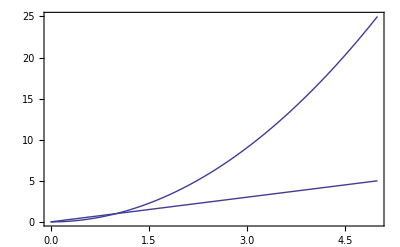

```mathematica
p1=Plot[x^2,{x,0,5}];
p2=Plot[x,{x,0,5}];
Show[p1,p2,Frame->True]
```

## Miscellaneous

This is a collection of miscellaneous commands and functions explained, that should be useful to you in your demonstrations.

### Entering constants, equations, and functions

Typically an expression is suppressed (entering the expression in Mathematica won’t return an output) with a colon and equals sign :=, this is fine to use if you are not planning on submitting your notebook as a demonstration. This, according to Wolfram Demonstrations Project will slow down evaluation. Instead, to suppress an expression you should follow that expression with a semicolon ;.

```mathematica
k1=0.5; ra=k*Ca[t];
```

Another way to enter an expression without outputting anything once the expression is entered, however it will not suppress the expression like using a semicolon will. This will also hide any error messages associated with the expression or command. The following is an example taken from the Documentation Center that demonstrates this command well.

```mathematica
1/0
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
Quiet[1/0]
```

ComplexInfinity

### If statements

The format of the If command (inside the brackets) is condition, then, else. It can be used in a number of scenarios such as in a simple function like the one shown below. It is useful in demonstrations too, a second example of this is shown below under ‘Making manipulated variables inactive’.

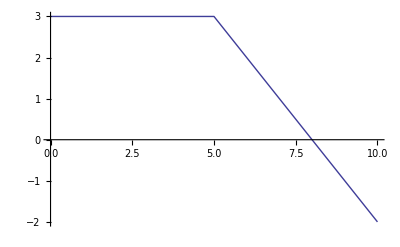

```mathematica
f[x_]=If[x≤5,3,8-x];
Plot[f[x],{x,0,10}]
```

### Control number of digits displayed

This function is helpful when you want to display a value and control how many digits are shown. If you didn’t need to control the number of digits displayed, you would simply write the variable itself like the first example shown below.

```mathematica
Ca0=0.205619;
Row[{"C_(A, 0) = ",Ca0}]
```

C_(A, 0) = 0.205619

Now using NumberForm you can limit the digits displayed for “Caing” to 3.

```mathematica
Row[{"C_(A, 0) = ",NumberForm[Ca0,3]}]
```

C_(A, 0) = 0.206

### Select a solution from a list *important*

What is [[n]]?
[[n]] is the same as Part[expression,n] where n is a whole number, typically 1. It’s easier to just use [[n]]. Here is an example of what it’ll do.

```mathematica
s=NSolve[x^2-2==0,x]
```

{{x→-1.41421},{x→1.41421}}

There are two solutions to this equation, which Mathematica displays in a list. Use s[[1]] (or First[s]) to get the first solution and s[[2]] will return the second solution.

```mathematica
s[[1]]
s[[2]]
```

{x→-1.41421}

{x→1.41421}

### Localize variables for faster evaluations

There are a few other ways to localize variables rather than using Module. For a detailed explanation of each of the three ways and the differences between them, see this post on Stack Exchange. The first is Block and the second is With:

Block is contructed the same way as Module.

```mathematica
Manipulate[
Block[{a,b},
	a=1; b=2;
	Plot[a*x^b+c,{x,0,5}]
	],
{{c,0,"y-intercept"},0,10}
]
```

With is similar to Module in the sense that it will localize defined variables. With is faster than Module.

```mathematica
With[
	{f=Subscript[f, 0]}, (*define local variable f*)
	10+f^2] (*some function/expression containing variable f*)
(*notice how now that f is defined as a local variable, it appears green. The same happens when Module is used to localize variables.*)
```

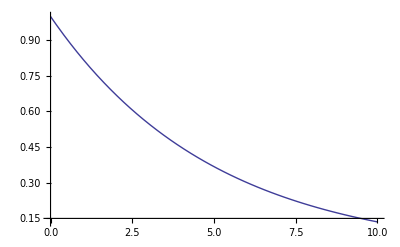

```mathematica
With[
{k=0.2,
s=NDSolve[{ (*the local variable 's' is defined here inside the curly brackets {}*)
Ca'[t]==-k*Ca[t],
Ca[0]==1},Ca,{t,0,10}]},
Plot[Ca[t]/.s,{t,0,10}] (*the fuction is Plot, where ever 's' is used, the local variable 's' will be used in its place*)
]
```

## Partial differential equations (PDE) in Mathematica

### Writing PDE’s in Mathematica

(∂^2 f[x,y])/(∂x^2)=x (∂f[x,y])/(∂y)+(∂f[x,y])/(∂x)-f[x,y]

Below are two examples of how the PDE can be written, note that both methods will return the same function.

```mathematica
D[function,{variable,order wrt variable}]
```

```mathematica
D[f[x,y],{x,2}]==x*D[f[x,y],y]+D[f[x,y],x]-f[x,y];
```

```mathematica
Derivative[order wrt var 1,order wrt var 2][function][var 1,var 2]
```

```mathematica
Derivative[2,0][f][x,y]==x*Derivative[0,1][f][x,y]+Derivative[1,0][f][x,y]-f[x,y];
```

This method is nice when you want to take the derivative of a function at a specific point, for example:

```mathematica
f[x_,y_,z_]=((y+1)^2*(z+1)^2)/2+Exp[y*z]*x^2;
Derivative[1,0,0][f][1,2,2];
```

“The first derivative of f with respect to x at the point (1,2,2).”

### Solving PDE’s in Mathematica

PDE’s are solved the same way you would solve an ODE, using NDSolve.

```mathematica
(*entering the PDE's*)
PDE={
D[f[x,t],x]==D[f[x,t],t]+f[x,t],
D[g[x,t],x]==t*D[g[x,t],t]};
(*entering initial and boundary conditions (must be equal*)
initialconditions={
f[x,0]==fo,
g[x,0]==go};
boundaryconditions={
f[0,t]==fo,
g[0,t]==go};
(*solve using NDSolve*)
solution=NDSolve[{
PDE,
initialconditions,
boundaryconditions},
{f,g},
{x,0,x1},{t,0,t1}];
```

## Nonlinear Models

### Nonlinear fit of data to rate law

#### Fitting the model

```mathematica
(*data has form {Ca,Cb,ra}*)
data={
{1,1,0.05},
{1,2,0.071},
{2,3,0.17},
{0.5,2,0.035},
{4,5.5,0.47},
{1.5,4,0.15},
{6.4,2,0.45},
{6,4,0.6}};
sol=NonlinearModelFit[data,
k*Ca^n*Cb^m,(*model you're fitting (ra)*)
{k,n,m},(*variables that need to be calculated/determined*)
{Ca,Cb},(*known variables*)
MaxIterations->200]
sol["ParameterConfidenceIntervalTable"]
sol["FitResiduals"]
```

FittedModel[0.0491168 Ca^1.00319 Cb^0.50875]

| Estimate | Standard Error | Confidence Interval
k | 0.0491168 | 0.000411467 | {0.0480591,0.0501745}
n | 1.00319 | 0.00362393 | {0.993872,1.0125}
m | 0.50875 | 0.00357849 | {0.499551,0.517948}

{0.000883204,0.00111581,-0.00216895,0.000135018,0.000248324,0.000658535,0.000086981,-0.0000112835}

#### Plotting the residuals

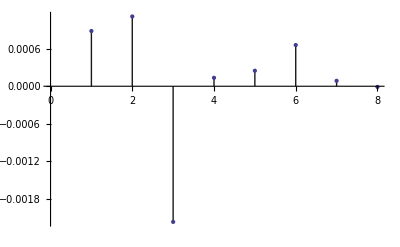

```mathematica
ListPlot[sol["FitResiduals"],
Filling->Axis,
FillingStyle->Opacity[0.9],
PlotStyle->Thick]
```

#### 3D Plot and points

Plot the data points onto the functions Ca and Cb to see how good the fit is.

```mathematica
plot1=Plot3D[sol[Ca,Cb],{Ca,0,7},{Cb,0,7},
PlotRange->All,
AxesLabel->Automatic];
plot2=ListPointPlot3D[data,
PlotRange->All,
PlotStyle->PointSize[Large]];
Show[plot1,plot2]
```

-Graphics3D-

### Nonlinear fit of data

#### No scatter example

```mathematica
(*data in form of {x,y,z}*)
nsdata={
{1,2,7},
{2,4,16},
{3,6,27},
{5,10,55},
{8,16,112},
{10,20,160}};
nssol=FindFit[nsdata,b*x^a+c*y^d,{
{a,3},(*this is saying the initial guess for a is 3*)
{b,2},
{c,2},
{d,1.5}},{x,y}]
```

{a→2.,b→1.,c→3.,d→1.}

## What you need to have in a demonstration before submitting

On the Wolfram Demonstrations Project guidelines page, there is a short guide to creating interactive demonstrations. Below are some additional guidelines that you should keep in mind while making your own demonstrations to submit.

•	In title, lowercase for these words: a, an, the, by, with, of, to, for, on, between, etc.
•	No “ := “, just use “ = “ and suppress the function with a semicolon “ ; “ at the 	end; using  :=  slows down evaluation.
•	No Arial fonts or any font that is not the default
•	No wobbly plots, set a PlotRange or use ImagePadding.
•	Nothing should be capitalized (unless proper noun or acronym) in the manipulate window.
•	Make sure all variables that are displayed in the manipulate window are explained.
•	If you’re displaying a variable in the manipulate window, it must be italicized
		example: “P = 10 bar”
•	Subscripts, Superscripts, Subsuperscripts, Italic, and Bold that is written in the code need to be written completely without the use of keyboard shortcuts. Note that outside of the code (ie in the 	Caption or Details sections) keyboard shortcuts should be used.
		Keyboard shortcut:	 x+Ctrl+6+2   ⟶  x^2
		Proper way to write:   Superscript[“x”,”2”]  ⟶  x^2
•	If any variables are written in the Caption or Details sections, select each individually and do Ctrl+9, below is an example pulled from the Details section, it shows what it looks like before using 		Ctrl+9, after it was done, and how it was done.
		old:
		where P is pressure, R is the ideal gas constant, T is temperature, V_m is the relative volume,  a, b, α, and κ are Peng-Robinson constants, P_c is the critical pressure, T_c is the critical 		temperature, and ω is the acentric factor. 
		new:
		where P is pressure, R is the ideal gas constant, T is temperature, V_m is the relative volume,  a, b, α, and κ are Peng-Robinson constants, P_c is the critical pressure, T_c is the 			critical temperature, and ω is the acentric factor. 
		
		how:
		select P, do Ctrl-9
		select R, do Ctrl-9
		select K, do Ctrl-I or command-I (Windows/Mac)
		select T, do Ctrl-9
		select  a, b, α, and κ separately, do Ctrl-9 on each one separately
		select ω, do Ctrl-9
		
		Any variables with a super-, or subscript will already be in the correct form.

## Troubleshooting tips

When you encounter an error message (of any kind) before you open up the Documentation Center and try to address the problem head on, try these quick and easy troubleshooting tips first. You’re problem may be an easier fix than you expected.

First go to the toolbar at the top, select Evaluation → Quit Kernel → Local. A window will pop up asking if you’re sure you want to quit the kernel, say Yes. Then re-evaluate your notebook. If this solves the problem then some of your variables likely had already been defined more than once, possibly from another notebook. This will clear that.

Another more obvious (but often overlooked) solution is to make sure you have all the commands in the right format. This is an easy mistake to make. You might have an = sign where you should have a == sign or vice versa. Or a comma instead of a semicolon. These mistakes may not be as obvious, when you’re missing a closing bracket or curly bracket, Mathematica will tell you after evaluating the cell.

When you’ve made sure that the error isn’t fixed from any of the above, easier fixes, copy and paste the code into a new window and start eliminating unnecessary portions of it, this way it’s easier to see where the problem is coming from. From here it’s usually a good idea to work through the math by hand to make sure it all makes sense and you aren’t trying to evaluate something illegal (like 1/0).